```mathematica
(*Peres Mermin Magic Square Stuff*)
```

```mathematica
X=({{0, 1}, {1, 0}});Z=({{1, 0}, {0, -1}});Y=({{0, -I}, {I, 0}});
```

```mathematica
KroneckerProduct[IdentityMatrix@2,Z]
```

{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
MRow1=Eigenvectors[KroneckerProduct[IdentityMatrix@2,X]+2KroneckerProduct[X,IdentityMatrix@2]]
```

{{1,-1,-1,1},{1,1,1,1},{-1,-1,1,1},{-1,1,-1,1}}

```mathematica
MRow2=Eigenvectors[KroneckerProduct[IdentityMatrix@2,Z]+2KroneckerProduct[Z,IdentityMatrix@2]]
```

{{0,0,0,1},{-1,0,0,0},{0,0,-1,0},{0,1,0,0}}

```mathematica
MRow3=Eigenvectors[KroneckerProduct[X,Z]+2KroneckerProduct[Z,X]]
```

{{-1,1,1,1},{-1,-1,-1,1},{1,-1,1,1},{1,1,-1,1}}

```mathematica
MCol1=Eigenvectors[KroneckerProduct[IdentityMatrix@2,X]+2KroneckerProduct[Z,IdentityMatrix@2]]
```

{{0,0,-1,1},{1,1,0,0},{0,0,1,1},{-1,1,0,0}}

```mathematica
MCol2=Eigenvectors[KroneckerProduct[IdentityMatrix@2,Z]+2KroneckerProduct[X,IdentityMatrix@2]]
```

{{0,-1,0,1},{1,0,1,0},{-1,0,1,0},{0,-1,0,-1}}

```mathematica
MCol3=Eigenvectors[KroneckerProduct[X,X]+2KroneckerProduct[Z,Z]]
```

{{0,-1,1,0},{1,0,0,1},{0,1,1,0},{-1,0,0,1}}

```mathematica
PMVectors=Union[MRow1,MRow2,MRow3,MCol1,MCol2,MCol3]
```

{{-1,-1,-1,1},{-1,-1,1,1},{-1,0,0,0},{-1,0,0,1},{-1,0,1,0},{-1,1,-1,1},{-1,1,0,0},{-1,1,1,1},{0,-1,0,-1},{0,-1,0,1},{0,-1,1,0},{0,0,-1,0},{0,0,-1,1},{0,0,0,1},{0,0,1,1},{0,1,0,0},{0,1,1,0},{1,-1,-1,1},{1,-1,1,1},{1,0,0,1},{1,0,1,0},{1,1,-1,1},{1,1,0,0},{1,1,1,1}}

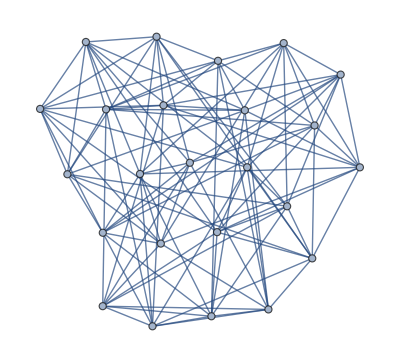

```mathematica
pmGraph=orthogonalityGraph@PMVectors
```

```mathematica
FindIndependentVertexSet[pmGraph,Infinity,All]
```

{{3,20,21,23,24},{3,20,22,23,24},{13,14,18,20,22},{10,13,14,18,20},{3,19,20,21,24},{10,14,18,19,20},{12,15,17,21,24},{2,4,10,14,15},{12,15,19,21,24},{15,19,20,21,24},{14,15,19,20,24},{10,14,15,19,20},{2,10,14,15,19},{11,12,15,19,21},{6,11,12,19,21},{6,11,12,13,22},{6,11,12,13,21},{2,11,12,15,19},{2,11,16,22,23},{2,10,11,15,19},{2,10,11,16,23},{2,10,11,16,19},{9,16,17,23,24},{9,14,15,20,24},{4,6,9,13,14},{9,16,22,23,24},{9,11,16,22,23},{9,20,22,23,24},{9,14,20,22,24},{9,13,14,20,22},{6,9,13,14,22},{6,9,11,16,22},{6,9,11,13,22},{8,12,15,17,24},{2,4,8,14,15},{8,9,16,17,24},{8,9,15,17,24},{8,9,14,15,24},{4,8,9,14,15},{4,6,8,9,14},{3,7,19,20,21},{3,7,18,19,20},{7,8,16,17,18},{7,8,9,16,17},{7,10,18,19,20},{7,10,11,16,19},{7,10,16,18,19},{7,10,16,17,18},{6,7,11,19,21},{6,7,11,16,19},{6,7,9,11,16},{6,7,8,9,16},{4,6,7,8,9},{3,6,7,19,21},{3,4,6,7,21},{3,4,6,7,8},{3,5,20,22,23},{3,5,18,20,22},{5,8,12,17,18},{5,8,12,15,17},{5,13,18,20,22},{5,11,12,13,22},{5,12,13,18,22},{5,12,13,17,18},{5,7,8,17,18},{3,5,7,18,20},{3,5,7,8,18},{3,4,5,7,8},{2,4,5,8,15},{2,5,8,12,15},{2,5,11,22,23},{2,5,11,12,22},{2,5,11,12,15},{2,3,5,22,23},{2,3,4,5,23},{2,3,4,5,8},{1,3,21,23,24},{1,10,13,14,18},{1,17,21,23,24},{1,10,13,17,18},{1,16,17,23,24},{1,2,10,16,23},{1,10,16,17,23},{1,10,16,17,18},{1,12,17,21,24},{1,6,12,13,21},{1,12,13,17,21},{1,12,13,17,18},{1,3,4,21,23},{1,4,10,13,14},{1,3,4,6,21},{1,4,6,13,21},{1,4,6,13,14},{1,2,3,4,23},{1,2,4,10,23},{1,2,4,10,14},{12,22,24},{16,18,22},{2,14,22},{3,6,22},{10,20,23},{13,20,21},{16,19,24},{6,14,19},{12,18,19},{2,3,19},{10,15,17},{4,15,21},{11,21,23},{10,11,13},{9,13,17},{9,11,15},{4,9,23},{3,8,24},{2,8,16},{8,14,18},{6,8,12},{7,9,20},{7,17,21},{4,7,10},{5,15,20},{5,17,23},{4,5,13},{5,7,11},{1,14,24},{1,3,18},{1,6,16},{1,2,12}}

```mathematica
modifiedPM=VertexDelete[pmGraph,1];
```

```mathematica
FindIndependentVertexSet[modifiedPM,Infinity,All];
```

```mathematica
contexts=Sort[Sort/@FindClique[pmGraph,Infinity,All]]
```

{{1,5,9,19},{1,7,15,22},{1,8,11,20},{1,8,19,22},{2,6,17,20},{2,6,18,24},{2,7,13,24},{2,9,18,21},{3,9,10,12},{3,11,14,17},{3,12,14,16},{3,13,15,16},{4,11,17,20},{4,11,18,24},{4,12,16,20},{4,17,19,22},{5,6,10,24},{5,9,10,21},{5,14,16,21},{6,15,18,23},{7,12,14,23},{7,13,15,23},{8,10,21,22},{8,13,19,23}}

```mathematica
completenessTest[removedSet_,iSet_,contexts_:contexts]:=And@@Or@@@Outer[MemberQ,contexts,Union[removedSet,iSet],1,1]
```

```mathematica
completenessTest[{1,19},#]&/@FindIndependentVertexSet[pmGraph,Infinity,All]
```

{True,False,False,True,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Or@@(completenessTest[{},#]&/@Subsets[Range[24],{7}])
```

True